```mathematica
ClearAll["Global`*"];
Needs["PX4ESC`","/home/pavel/projects/px4esc/px4esc_foc/tools/mathematica/PX4ESC.m"];

{time,data}=PX4ESC`splitXY[PX4ESC`parseFile["~/Namiki300-2.log"]];

breakingPoint=LengthWhile[Differences[data[[2]]],#>-10^-9&];
(*breakingPoint=550;*)
time=time[[breakingPoint;;-100]];
data=dataᵀ[[breakingPoint;;-100]]ᵀ;

dataPhi=data[[6]] 10^-3;
dataUdq={data[[1]],data[[2]]};
dataIdq={data[[3]],data[[4]]};
dataAngVel=data[[5]];

dataU=Map[Norm,dataUdqᵀ];
dataI=Map[Norm,dataIdqᵀ];
dataIFiltered=LowpassFilter[dataI,0.01];

ϕ:=(Udq-Idq Rs)/ω;
mapPhi[rs_]:=Map[ϕ/.{Udq->#[[1]],Idq->#[[2]],ω->#[[3]],Rs->rs}&,{dataU,dataI,dataAngVel}ᵀ];

linearFit[x_,y_]:=Module[{
sumX=Total[x],
sumY=Total[y],
sumXY=First[x.{y}ᵀ],
sumXX=First[x.{x}ᵀ],
n=Length[x],
slope
},
slope=(sumX*sumY-n*sumXY)/(sumX*sumX-n*sumXX);
{slope,(sumY-slope sumX)/n}
];

plotFit[x_,y_]:=Module[{coeffs=linearFit[x,y]},ListLinePlot[{{x,y}ᵀ,{x,Map[coeffs[[1]]#+coeffs[[2]]&,x]}ᵀ},PlotTheme->"Detailed"]];
```

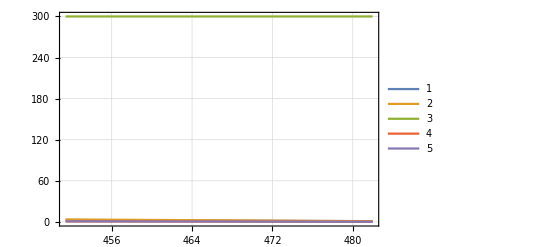

```mathematica
ListLinePlot[{{time,dataPhi 10^3}ᵀ,{time,dataUdq[[2]]}ᵀ,{time,dataAngVel}ᵀ,{time,dataI}ᵀ,{time,dataIFiltered}ᵀ},PlotTheme->"Detailed",PlotLegends->Automatic]
```

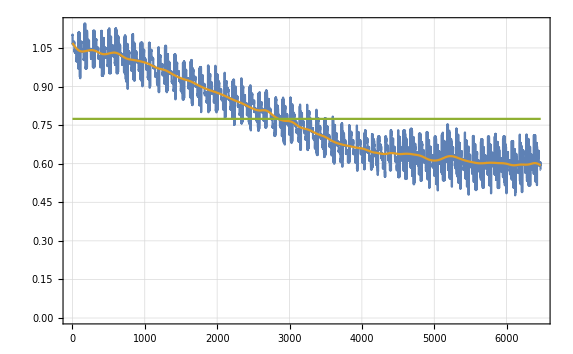

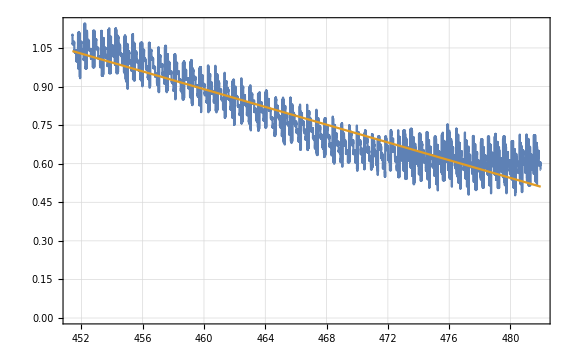

```mathematica
phi=mapPhi[4.1];
ListLinePlot[{phi 10^3,LowpassFilter[phi 10^3,.01],Table[Mean[phi] 10^3,Length[phi]]},PlotRange->{0,Automatic},PlotTheme->"Detailed",GridLines->Automatic]
plotFit[time,phi 10^3]
```

```mathematica
ClearAll[computeError3];
computeError1[rs_]:=Module[{phi=mapPhi[rs],linear},
linear=linearFit[time,phi];
Total[Map[((linear[[1]]#[[1]]+linear[[2]])-#[[2]])^2&,{time,phi}ᵀ]]/Length[phi]
];
computeError2[rs_]:=Module[{phi=mapPhi[rs],mean},
mean=Mean[phi[[-1000;;]]];
Total[Map[(mean-#)^2&,phi]]/Length[phi]
];
computeError3[rs_]:=Module[{},Abs[linearFit[time[[-1000;;]],mapPhi[rs][[-1000;;]]][[1]]]];
FindMinimum[computeError3[x],{x,1},AccuracyGoal->40,PrecisionGoal->50]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.26884×10^-12,{x→4.11008}}

```mathematica
Mean[Map[ϕ/.{Udq->#[[1]],Idq->#[[2]],ω->#[[3]],Rs->4.2}&,{dataU[[-100;;]],dataI[[-100;;]],dataAngVel[[-100;;]]}ᵀ]] 10^3
```

0.538653

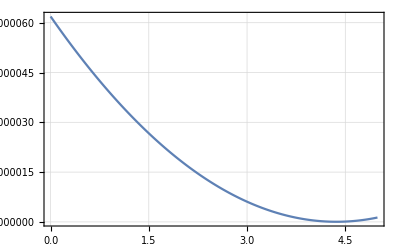

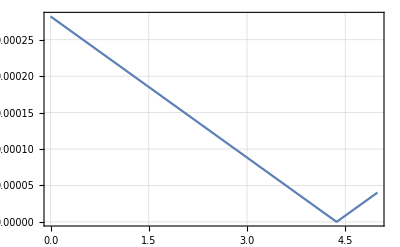

```mathematica
ListLinePlot[ParallelMap[{#,computeError2[#]}&,Range[0.001,5,0.01]],PlotTheme->"Detailed"]
ListLinePlot[ParallelMap[{#,computeError3[#]}&,Range[0.001,5,0.01]],PlotTheme->"Detailed"]
```